# 傅里叶级数

```mathematica
tf[expr_,x_,m_]:=Table[FourierSeries[expr,x,i],{i,m}]
```

### 近似描述一个分段函数

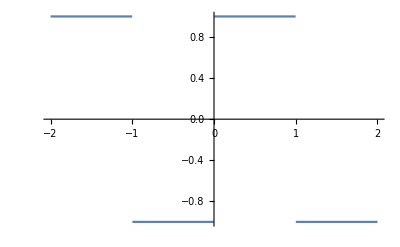
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[#,{x,-2,2}]&/@{(-1)^Floor[x],Sign[Sin[Pi x]],1-2Floor@Mod[x,2],Cos[Floor@x Pi]}
```

```mathematica
lss=tf[Sign@Sin[Pi x],x,20];
```

```mathematica
Manipulate[Plot[{Sign@Sin[Pi x],lss[[m]]},{x,-2,2},PlotRange->1.5],{m,1,20,1}]
```

### 近似描述 x^2

```mathematica
lx2=tf[x^2,x,20];
```

```mathematica
Manipulate[Plot[{x^2,lx2[[m]]},{x,-2,2},PlotRange->{{-2,2},{-1,4}}],{m,1,20,1}]
```